This for single Reed.

```mathematica
Clear["Global`*"]
```

```mathematica
c1=1.5 Sqrt[3];
```

```mathematica
(*vdotMax:=(2/3)*w*h0*Sqrt[(2*ΔPMax)/(3*ρ)];
ΔPMax:=(h0*kReed)/ASurface; *)
```

The above are equations relating valve parameters to flow parameter. For now, I will normalize them to be 1

```mathematica
vdotMax=2;ΔPMax=1;
```

```mathematica
a=1/6;b=1/6;c=2Pi;d=0.02;sigma=1;
```

```mathematica
(*sin*)deltaPReed[t_]:=Sin[c*t]*a+b;
```

```mathematica
(*square wave*)deltaPReed[t_]:=a*SquareWave[c*t]+b+a;
```

```mathematica
(*Triangular wave*)deltaPReed[t_]:=a*TriangleWave[c*t]+b+a;
```

```mathematica
(*Sawtooth wave*)deltaPReed[t_]:=a*SawtoothWave[c*t]+b+a;
```

```mathematica
(*Linear, for checking*)deltaPReed[t_]:=t-1;
```

```mathematica
(*Linear + sin, for seeing realistic *)deltaPReed[t_]:=Sin[c*t]*a+d*t+b
```

```mathematica
(*Periodic gaussian*)deltaPReed[t_]:=a*Sin[2*Pi*c*t]*Exp[-(Mod[t,1/c]-0.5/c)^2/(2*sigma^2)]+b;
```

```mathematica
(*generic wave 1*)deltaPReed[t_]:=a*Sin[20*c*t]+(1+1*SquareWave[c*t])+b
```

```mathematica
vReedDot[t_]:=Module[{deltaP},deltaP=deltaPReed[t];(*ΔP_reed(t)*)Piecewise[{{-c1 vdotMax √(1/ΔPMax) √Abs[deltaP],deltaP<=0},{c1*vdotMax*(1-deltaP/ΔPMax)*Sqrt[deltaP/ΔPMax],0<deltaP<ΔPMax},{0,deltaP>=ΔPMax}}]] (*Add a linear continuation of the positive resistance, do Series[c1*vdotMax*(1-deltaP/ΔPMax)*Sqrt[deltaP/ΔPMax],{deltaP,0,3}] and take the first term, note that I used t*)
```

for sin waves (a=0.3;b=0.15;c=2Pi/4;), this will produce plot 3.19 in Jacob. 
square waves with parameter (a=0.3;b=0.15;c=1/4) have pretty non-distinctive features (as expected)
triangle wave yield similar behavior to sin wave

### below we model the behavior of

```mathematica
tf = 10;
vLines=Table[{Dashed,Gray,Line[{{t,-Infinity},{t,Infinity}}]},{t,{2,4,6,8,10}}];


(*use 3.44 in Jacob to get power, just consider the flow across the valve*)


p1=Plot[deltaPReed[t],{t,0,tf},Frame->True,FrameLabel->{"Time t","ΔP"},PlotLabel->"Shape of Pressure vs Time",PlotStyle->Red,Epilog->vLines,BaseStyle->{FontFamily->"Helvetica",FontSize->12}]

p2=Plot[vReedDot[t],{t,0,tf},Frame->True,FrameLabel->{"Time t","Volumetric Flow Rate"},PlotLabel->"Volumetric Flow Rate vs Time",PlotStyle->Blue,Epilog->vLines,BaseStyle->{FontFamily->"Helvetica",FontSize->12}]

p3=Plot[vReedDot[t]*deltaPReed[t],{t,0,tf},Frame->True,FrameLabel->{"Time t",""},PlotLabel->"Power vs Time",PlotStyle->Green,Epilog->vLines,BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

-Graphics-

-Graphics-

-Graphics-

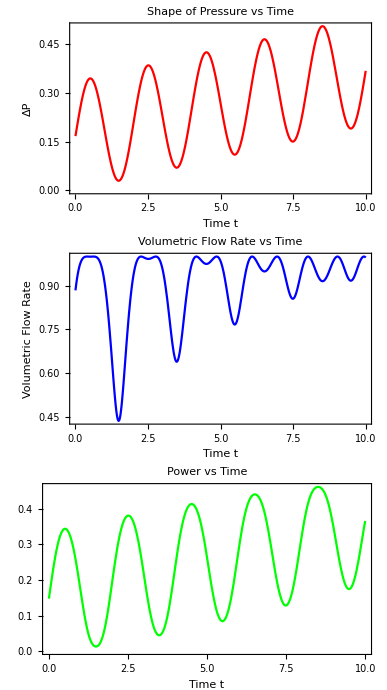

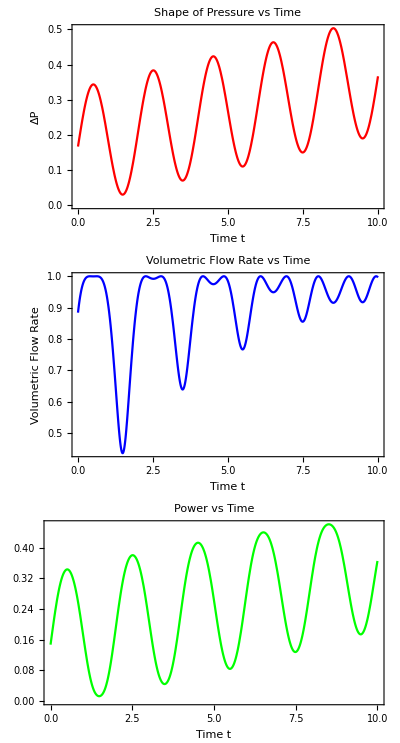

```mathematica
Export["/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/square.pdf",%394,"PDF"]
```

/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/square.pdf

```mathematica
Export["/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/sin.pdf",%385,"PDF"]
```

/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/sin.pdf

```mathematica
Export["/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/square+sin.pdf",%355,"PDF"]
```

/Users/a1/Desktop/acoustic project/Flow_Power_with_input_pressure/square+sin.pdf

average mass flow vs. amplitude of oscillation.

```mathematica
FunctionPeriod[Sin[2Pi x],x]
```

1